## 积分初步

### 积分的引入

积分跟导数一样，也有很直观的几何意义。一般了解积分，是从算面积开始的。
例如我们有一条曲线，y=Sin[π x]. 当然拿到曲线，我们想了解一下这个曲线是什么样子的。

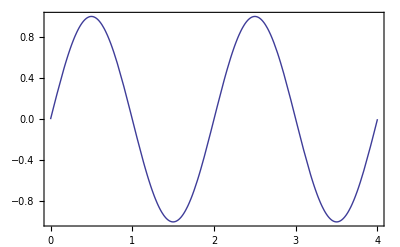

```mathematica
intEg1Plt1=Plot[Sin[π x],{x,0,4},AxesOrigin->{0,0},Frame->True]
```

这是一个周期为 2 的函数。那么一个问题是，在 [0,1] 内这个函数跟横轴围成的图形的面积是什么。即下面加阴影的部分。

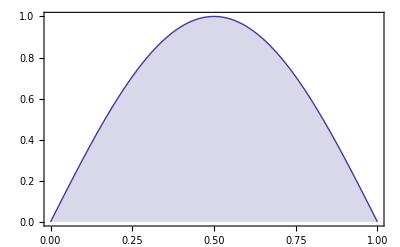

```mathematica
intEg1Plt2=Plot[Sin[π x],{x,0,1},AxesOrigin->{0,0},Filling->Axis,Frame->True]
```

这样一个复杂的形状怎么算呢？我们只会算基本形状的面积，比如我们最擅长的是算长方形的面积。所以我们可以试着用长方形来近似。

（建立绘制分片的函数，http://demonstrations.wolfram.com/RiemannSums/ ）

```mathematica
LeftValue[f_,{x_,a_,b_}]:=N[f/.x->a];
MidpointValue[f_,{x_,a_,b_}]:=N[f/.x->(a+b)/2];
RightValue[f_,{x_,a_,b_}]:=N[f/.x->b];
Sample[f_,{x_,a_,b_},type_]:={LeftValue[f,{x,a,b}],MidpointValue[f,{x,a,b}],RightValue[f,{x,a,b}]}[[type]];
BlockCoords[a_,b_,h_]:={{a,0},{a,h},{b,h},{b,0}};
IsReal[x_]:=Module[{},If[!NumericQ[x]||Im[x]!=0,Throw["One or more samples are outside the domain."]];x];
RiemannBlocks[f_,{x_,a_,b_,n_},type_]:=Plot[f,{x,a,b},Prolog->Table[({{GrayLevel[0.8],Polygon[#1]},Line[Append[#1,#1[[1]]]]}&)[(BlockCoords[#1,#2,Sample[f,{x,#1,#2},type]]&)[a+i*((b-a)/n),a+(i+1)*((b-a)/n)]],{i,0,n-1}],Frame->True]
```

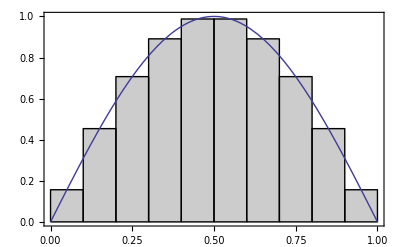

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,10},2]
```

这样我们可以大致算出这个奇怪的图像的面积了。每个长方形宽度都是Δx，而在x=xi处的长方形的高度为f(xi)，那么这个长方形的面积为，Δx*f(xi)。这样我们只需要把所有长方形的面积加起来：∑Δx*f(xn)
但是如何从估算到精确计算呢？
如果我们分割的更小呢？上面只有10个分割，我们分割成50个。

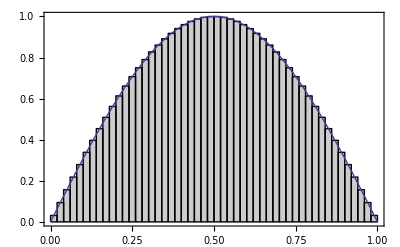

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,50},2]
```

这样我们的估算就变得越来越精确。倘若我们能够让每个分割足够小，我们就可以精确的计算了。我们用 dx 来表示无穷小的分割，即dx为长方形的宽度，而位于x处的长方形的高度可以直接写成 f(x)，这个无穷小的长方形的面积是 f(x)dx，那么我们需要把所有的这些长方形加起来就可以了。我们把这个求和写成：
(∫_0)^1 f(x)dx

实际上这就是积分了。
也就是说，积分像是一种特殊的求和运算。

### 积分

当然数学上不能这么马虎，需要严格仔细的定义。关于可加性，关于使用极限的方法来严格定义，还需要自己阅读课本。当然实际上积分定义的时候用线性代数的方法比较简洁，这里不详细说了。